```mathematica
(*Numerical Calculation*)
```

```mathematica
ClearSystemCache[];
a0 = 1/(√2);a1 = 1/(√2);ħ=(6.62607004*10^-34)/(2*Pi);m=40.078*1.660539040*10^-27;ω=2*Pi*10^6;ωx=2*Pi*1.0*10^6;ωy=2*Pi*2.5*10^6;ωz=2*Pi*2.5*10^6;
scale = 6*10^-8;
change=1;
Psi0[ω_,x_]:=√(1/2^0)*((m*ω)/(Pi*ħ))^(1/4)*Exp[(-m*ω*x^2)/(2*ħ)]*HermiteH[0,√((m*ω)/ħ)*x];
Psi1[ω_,x_]:=√(1/2^1)*((m*ω)/(Pi*ħ))^(1/4)*Exp[(-m*ω*x^2)/(2*ħ)]*HermiteH[1,√((m*ω)/ħ)*x];
f0[x_,y_,z_]:=Psi0[ωx,x]*Psi0[ωy,y]*Psi0[ωz,z];f1[x_,y_,z_]:=Psi1[ωx,x]*Psi0[ωy,y]*Psi0[ωz,z];
V00[x1,y1,z1,x2,y2,x2]:=(((f0[x2,y2,x2])^2*a0^2+(f1[x2,y2,z2])^2*a1^2)/(√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2)))*(f0[x1,y1,x1])^2;
V11[x1,y1,z1,x2,y2,x2]:=(((f0[x2,y2,x2])^2*a0^2+(f1[x2,y2,z2])^2*a1^2)/(√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2)))*(f1[x1,y1,x1])^2;Print[Timing[NIntegrate[(V00[x1,y1,z1,x2,y2,x2])* Boole[(x1-x2)^2+(y1-y2)^2+(z1-z2)^2>0],{x1,-scale,scale},{y1,-scale,scale},{z1,-scale,scale},{x2,-scale,scale},{y2,-scale,scale},{z2,-scale,scale},Method->{"AdaptiveMonteCarlo","MaxPoints"->5*10^7,"RandomSeed"->Automatic},AccuracyGoal->6,PrecisionGoal->8]]];(*Clear[scale,a0,a1,ħ,m,temp,temp2,ω,ωx,ωy,ωz,change];*)
```

NIntegrate::maxp: The integral failed to converge after 50000100 integrand evaluations. NIntegrate obtained 2.90752×10^8 and 62583.1 for the integral and error estimates.

{93.,2.90752×10^8}

```mathematica
ClearSystemCache[];
a0 = 1/(√2);a1 = 1/(√2);ħ=(6.62607004*10^-34)/(2*Pi);m=40.078*1.660539040*10^-27;ω=2*Pi*10^6;ωx=2*Pi*1.0*10^6;ωy=2*Pi*2.5*10^6;ωz=2*Pi*2.5*10^6;
scale =6*10^-8;
change=1;
Psi0[ω_,x_]:=√(1/2^0)*((m*ω)/(Pi*ħ))^(1/4)*Exp[(-m*ω*x^2)/(2*ħ)]*HermiteH[0,√((m*ω)/ħ)*x];
Psi1[ω_,x_]:=√(1/2^1)*((m*ω)/(Pi*ħ))^(1/4)*Exp[(-m*ω*x^2)/(2*ħ)]*HermiteH[1,√((m*ω)/ħ)*x];
f0[x_,y_,z_]:=Psi0[ωx,x]*Psi0[ωy,y]*Psi0[ωz,z];f1[x_,y_,z_]:=Psi1[ωx,x]*Psi0[ωy,y]*Psi0[ωz,z];
V00[x1,y1,z1,x2,y2,x2]:=(((f0[x2,y2,x2])^2*a0^2+(f1[x2,y2,z2])^2*a1^2)/(√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2)))*(f0[x1,y1,x1])^2;
V11[x1,y1,z1,x2,y2,x2]:=(((f0[x2,y2,x2])^2*a0^2+(f1[x2,y2,z2])^2*a1^2)/(√((x1-x2)^2+(y1-y2)^2+(z1-z2)^2)))*(f1[x1,y1,x1])^2;Print[Timing[NIntegrate[(V00[x1,y1,z1,x2,y2,x2])* Boole[(x1-x2)^2+(y1-y2)^2+(z1-z2)^2>0],{x1,-scale,scale},{y1,-scale,scale},{z1,-scale,scale},{x2,-scale,scale},{y2,-scale,scale},{z2,-scale,scale},Method->{"GlobalAdaptive","MaxErrorIncreases"->50000},MinRecursion->10,MaxRecursion->3000]]];(*Clear[scale,a0,a1,ħ,m,temp,temp2,ω,ωx,ωy,ωz,change];*)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 50000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.97547×10^8 and 3.55375×10^7 for the integral and error estimates.

{97.25,2.97547×10^8}

```mathematica
(*Analytical Calculation*)
```

```mathematica
Subscript[ψ, 0]=√(1/2^0)*((m*ωx)/(Pi*ħ))^(1/4)*Exp[(-m*ωx*x^2)/(2*ħ)]*HermiteH[0,√((m*ωx)/ħ)*x]*√(1/2^0)*((m*ωy)/(Pi*ħ))^(1/4)*Exp[(-m*ωy*y^2)/(2*ħ)]*HermiteH[0,√((m*ωy)/ħ)*y]*√(1/2^0)*((m*ωz)/(Pi*ħ))^(1/4)*Exp[(-m*ωz*z^2)/(2*ħ)]*HermiteH[0,√((m*ωz)/ħ)*z]=(ⅇ^(-(m (x^2 ωx+y^2 ωy+z^2 ωz))/(2 ħ)) ((m ωx)/ħ)^(1/4) ((m ωy)/ħ)^(1/4) ((m ωz)/ħ)^(1/4))/π^(3/4)
```

```mathematica
Subscript[ψ, 1]=(√2 ⅇ^(-(m (x^2 ωx+y^2 ωy+z^2 ωz))/(2 ħ)) x ((m ωx)/ħ)^(3/4) ((m ωy)/ħ)^(1/4) ((m ωz)/ħ)^(1/4))/π^(3/4)
```

```mathematica
Subscript[ψ, 2]=-(ⅇ^(-(m (x^2 ωx+y^2 ωy+z^2 ωz))/(2 ħ)) ((m ωx)/ħ)^(1/4) (ħ-2 m x^2 ωx) ((m ωy)/ħ)^(1/4) ((m ωz)/ħ)^(1/4))/(ħ π^(3/4))
```

```mathematica
Subscript[simpleψ, 0]=((m ω)/(π*ħ))^(3/4)*ⅇ^(-(m *ω*(x^2+y^2+z^2))/(2 ħ))
```

```mathematica
Subscript[simpleψ, 1]=((m ω)/ħ)^(1/2)*√2*x*((m ω)/(π*ħ))^(3/4)*ⅇ^(-(m *ω*(x^2+y^2+z^2))/(2 ħ))
```

```mathematica
Subscript[simpleψ, 2]=-(ⅇ^(-(m (x^2+y^2+z^2) ω)/(2 ħ)) ((m ω)/ħ)^(3/4) (ħ-2 m x^2 ω) (ħ-2 m y^2 ω) (ħ-2 m z^2 ω))/(2 √2 ħ^3 π^(3/4))
```

```mathematica
Integrate[(((m ω)/ħ)^(1/2)*√2*x*((m ω)/(π*ħ))^(3/4)*ⅇ^(-(m *ω*(x^2+y^2+z^2))/(2 ħ)))^2,{x,-Infinity,Infinity},{y,-Infinity,Infinity},{z,-Infinity,Infinity}]
```

ConditionalExpression[1, Re[(m ω)/ħ]>0]

```mathematica
Integrate[(-(ⅇ^(-(m (x^2+y^2+z^2) ω)/(2 ħ)) ((m ω)/ħ)^(3/4) (ħ-2 m x^2 ω) (ħ-2 m y^2 ω) (ħ-2 m z^2 ω))/(2 √2 ħ^3 π^(3/4)))^2,{x,-Infinity,Infinity},{y,-Infinity,Infinity},{z,-Infinity,Infinity}]
```

ConditionalExpression[1, Re[(m ω)/ħ]≥0]

```mathematica
V00=A00+B00
```

```mathematica
(4*Pi)/(4*Pi*r0^2)*∫_0^r0 (4*π*r^2*(((m ω)/(π*ħ))^(3/4)*ⅇ^(-(m *ω*(r^2))/(2 ħ)))^2)ⅆr
```

(√((m ω)/ħ) (-(2 ⅇ^(-(m r0^2 ω)/ħ) r0)/(√π)+(√ħ Erf[(√m r0 √ω)/(√ħ)])/(√m √ω)))/r0^2

```mathematica
A0=∫_r^Infinity ((√((m ω)/ħ) (-(2 ⅇ^(-(m r0^2 ω)/ħ) r0)/(√π)+(√ħ Erf[(√m r0 √ω)/(√ħ)])/(√m √ω)))/r0^2)ⅆr0
```

ConditionalExpression[1/2 √((m ω)/ħ) ((2 √ħ Erf[(√m r √ω)/(√ħ)])/(√m r √ω)+(Log[ħ/(m ω)]+Log[(m ω)/ħ])/(√π)), Re[r]>0&&Im[r]==0&&Re[(m ω)/ħ]>0]

```mathematica
A00=a0^2 *∫_0^Infinity (((m ω)/(π*ħ))^(3/4)*ⅇ^(-(m *ω*(r0^2))/(2 ħ)))^2*4*π*r0^2*(1/2 √((m ω)/ħ) ((2 √ħ Erf[(√m r0 √ω)/(√ħ)])/(√m r0 √ω)))ⅆr0
```

ConditionalExpression[(m^2 √(2/π) ω^2)/(ħ^2 ((m ω)/ħ)^(3/2)), Re[(m ω)/ħ]≥0&&Re[(√m √ω)/(√ħ)]>0]

```mathematica
A00 = a0^2 √(2/π) √((m ω)/ħ)
```

```mathematica
B00=a1^2 *Integrate[(((m ω)/ħ)^(1/2)*√2*r*Sin[φ]*Cos[θ]*((m ω)/(π*ħ))^(3/4)*ⅇ^(-(m *ω*(r^2))/(2 ħ)))^2*r^2*Sin[φ]*(1/2 √((m ω)/ħ) *(2 √ħ Erf[(√m r √ω)/(√ħ)])/(√m r √ω)),{r,0,Infinity},{φ,0,Pi},{θ,0,2*Pi}]
```

ConditionalExpression[(5 a1^2 m^3 ω^3)/(3 ħ^3 √(2 π) ((m ω)/ħ)^(5/2)), Re[(m ω)/ħ]≥0&&Re[(√m √ω)/(√ħ)]>0]

```mathematica
B00=(5 a1^2 √((m ω)/ħ))/(3 √(2 π))
```

```mathematica
V00=A00+B00=((6 a0^2+5 a1^2) √((m ω)/ħ))/(3 √(2 π))
```

((6 a0^2+5 a1^2) √((m ω)/ħ))/(3 √(2 π))

```mathematica
V11=A11+B11
```

```mathematica
A11~=B00~=(5 a0^2 √((m ω)/ħ))/(3 √(2 π));A11=(5 a0^2 √((m ω)/ħ))/(3 √(2 π))
```

```mathematica
(*2022.1.1 Analytical Calculation For B11*)
```

```mathematica
(*Consider the Integration of x First*)
```

```mathematica
Cos[θ]^2=(2 √π)/3*SphericalHarmonicY[0,0,θ,∅]+(4 √(π/5))/3*SphericalHarmonicY[2,0,θ,∅];
```

```mathematica
ψ1^2=(2 ⅇ^(-(m x^2 ω)/ħ) x^2 ((m ω)/ħ)^(5/2) ((2 √π)/3*SphericalHarmonicY[0,0,θ,∅]+(4 √(π/5))/3*SphericalHarmonicY[2,0,θ,∅]))/π^(3/2);
```

```mathematica
Part1=(2 ⅇ^(-(m x^2 ω)/ħ) x^2 ((m ω)/ħ)^(5/2) *(2 √π)/3*SphericalHarmonicY[0,0,θ1,∅1])/π^(3/2);
```

```mathematica
Part2=(2 ⅇ^(-(m x^2 ω)/ħ) x^2 ((m ω)/ħ)^(5/2)*(4 √(π/5))/3*SphericalHarmonicY[2,0,θ1,∅1])/π^(3/2);
```

```mathematica
Intx=∫_0^y ∫_0^Pi ∫_0^(2*Pi) (Part1*1/Abs[x-y]+Part2*1/Abs[x-y])ⅆxⅆθ1ⅆ∅1;
```

```mathematica
∫_0^y ∫_0^Pi ∫_0^(2*Pi) (Part1*1/Abs[x-y])x^2*Sin[θ1]ⅆxⅆθ1ⅆ∅1=∫_0^y ∫_0^Pi ∫_0^(2*Pi) (2 ⅇ^(-(m x^2 ω)/ħ) x^2 ((m ω)/ħ)^(5/2) *(2 √π)/3*SphericalHarmonicY[0,0,θ,∅])/π^(3/2)*1/y*∑_(l=0)^Infinity (x/y)^l*(4*Pi)/(2*l+1)*∑_(m=-l)^l SphericalHarmonicY[l,m,θ,∅]*SphericalHarmonicY[l,m,θ1,∅1]*x^2*Sin[θ1]ⅆxⅆθ1ⅆ∅1=∫_0^y ∫_0^Pi ∫_0^(2*Pi) (2 ⅇ^(-(m x^2 ω)/ħ) x^2 ((m ω)/ħ)^(5/2) *(2 √π)/3*SphericalHarmonicY[0,0,θ,∅])/π^(3/2)*1/y*(x/y)^0*(4*Pi)/(2*0+1)*SphericalHarmonicY[0,0,θ,∅]*SphericalHarmonicY[0,0,θ1,∅1]*x^2*Sin[θ1]ⅆxⅆθ1ⅆ∅1;
```

```mathematica
Integrate[(2 ⅇ^(-(m x^2 ω)/ħ) x^2 ((m ω)/ħ)^(5/2) *(2 √π)/3*SphericalHarmonicY[0,0,θ1,∅1])/π^(3/2)*1/y*(x/y)^0*(4*Pi)/(2*0+1)*SphericalHarmonicY[0,0,θ,∅]*SphericalHarmonicY[0,0,θ1,∅1]*x^2*Sin[θ1],{x,0,y},{θ1,0,Pi},{∅1,0,2*Pi}]
```

(((m ω)/ħ)^(3/2) (-(2 ⅇ^(-(m y^2 ω)/ħ) √m √ω (3 ħ+2 m y^2 ω))/(√π)+(3 ħ^(3/2) Erf[(√m y √ω)/(√ħ)])/y))/(3 m^(3/2) ω^(3/2))

```mathematica
∫_0^y ∫_0^Pi ∫_0^(2*Pi) (Part2*1/Abs[x-y])*x^2*Sin[θ1]ⅆxⅆθ1ⅆ∅1=∫_0^y ∫_0^Pi ∫_0^(2*Pi) (2 ⅇ^(-(m x^2 ω)/ħ) x^2 ((m ω)/ħ)^(5/2)*(4 √(π/5))/3*SphericalHarmonicY[2,0,θ1,∅1])/π^(3/2)*1/y*(x/y)^2*(4*Pi)/(2*2+1)*SphericalHarmonicY[2,0,θ,∅]*SphericalHarmonicY[2,0,θ1,∅1]*x^2*Sin[θ1]ⅆxⅆθ1ⅆ∅1
```

```mathematica
Integrate[(2 ⅇ^(-(m x^2 ω)/ħ) x^2 ((m ω)/ħ)^(5/2)*(4 √(π/5))/3*SphericalHarmonicY[2,0,θ1,∅1])/π^(3/2)*1/y*(x/y)^2*(4*Pi)/(2*2+1)*SphericalHarmonicY[2,0,θ,∅]*SphericalHarmonicY[2,0,θ1,∅1]*x^2*Sin[θ1],{x,0,y},{θ1,0,Pi},{∅1,0,2*Pi}]
```

(ⅇ^(-(m y^2 ω)/ħ) ((m ω)/ħ)^(3/2) (1+3 Cos[2 θ]) (-2 √m y √ω (15 ħ^2+10 ħ m y^2 ω+4 m^2 y^4 ω^2)+15 ħ^(5/2) ⅇ^((m y^2 ω)/ħ) √π Erf[(√m y √ω)/(√ħ)]))/(60 m^(5/2) √π y^3 ω^(5/2))

```mathematica
Intx=(((m ω)/ħ)^(3/2) (-(2 ⅇ^(-(m y^2 ω)/ħ) √m y √ω (15 ħ^2+70 ħ m y^2 ω+44 m^2 y^4 ω^2+3 (15 ħ^2+10 ħ m y^2 ω+4 m^2 y^4 ω^2) Cos[2 θ]))/(√π)+15 ħ^(3/2) (ħ+4 m y^2 ω+3 ħ Cos[2 θ]) Erf[(√m y √ω)/(√ħ)]))/(60 m^(5/2) y^3 ω^(5/2))
```

```mathematica
Integrate[a1^2*(2*2* ⅇ^(-(m y^2 ω)/ħ) y^2 ((m ω)/ħ)^(5/2) Cos[θ]^2)/π^(3/2)*(((m ω)/ħ)^(3/2) (-(2 ⅇ^(-(m y^2 ω)/ħ) √m y √ω (15 ħ^2+70 ħ m y^2 ω+44 m^2 y^4 ω^2+3 (15 ħ^2+10 ħ m y^2 ω+4 m^2 y^4 ω^2) Cos[2 θ]))/(√π)+15 ħ^(3/2) (ħ+4 m y^2 ω+3 ħ Cos[2 θ]) Erf[(√m y √ω)/(√ħ)]))/(60 m^(5/2) y^3 ω^(5/2))*y^2*Sin[θ],{y,0,Infinity},{θ,0,Pi},{∅,0,2*Pi}]
```

ConditionalExpression[(49 a1^2 √m √ω)/(30 √ħ √(2 π)), Re[(m ω)/ħ]≥0&&Re[(√m √ω)/(√ħ)]>0]

```mathematica
V11=(49 a1^2 √m √ω)/(30 √ħ √(2 π))+(5 a0^2 √((m ω)/ħ))/(3 √(2 π))=(50 a0^2 √((m ω)/ħ)+49 a1^2 √((m ω)/ħ))/(30 √(2 π))
```

```mathematica
V00-V11=((6 a0^2+5 a1^2) √((m ω)/ħ))/(3 √(2 π))-(50 a0^2 √((m ω)/ħ)+49 a1^2 √((m ω)/ħ))/(30 √(2 π))=((10 a0^2+a1^2) √((m ω)/ħ))/(30 √(2 π))
```

```mathematica
(*2022.1.2 Analytical Calculation For V01 & V10*)
```

```mathematica
ψ0ψ1=(√2 ⅇ^(-(m (x^2+y^2+z^2) ω)/ħ) m^2 x ω^2)/(ħ^2 π^(3/2))=(√2 ⅇ^(-(m (x^2) ω)/ħ) m^2 x*Cos[θ]*ω^2)/(ħ^2 π^(3/2));
```

```mathematica
1/Abs[x-y]=1/y*∑_(l=0)^Infinity (x/y)^l*(4*Pi)/(2*l+1)*∑_(m=-l)^l SphericalHarmonicY[l,m,θ,∅]*SphericalHarmonicY[l,m,θ1,∅1];
```

```mathematica
(*Consider the Integration of x First*)
```

```mathematica
Cos[θ]=1/(1/2*√(3/Pi))*SphericalHarmonicY[1,0,θ,∅]
```

```mathematica
intx=∫_0^Infinity ∫_0^Pi ∫_0^(2*Pi) 1/Abs[x-y]*ψ0ψ1*x^2*Sin[θ1]ⅆ∅1ⅆθ1ⅆx=∫_0^Infinity ∫_0^Pi ∫_0^(2*Pi) ψ0ψ1*(1/y*∑_(l=0)^Infinity (x/y)^l*(4*Pi)/(2*l+1)*∑_(m=-l)^l SphericalHarmonicY[l,m,θ,∅]*SphericalHarmonicY[l,m,θ1,∅1])*x^2*Sin[θ1]ⅆ∅1ⅆθ1ⅆx=∫_0^Infinity ∫_0^Pi ∫_0^(2*Pi) (√2 ⅇ^(-(m (x^2) ω)/ħ) m^2 x*Cos[θ1] ω^2)/(ħ^2 π^(3/2))*(1/y*∑_(l=0)^Infinity (x/y)^l*(4*Pi)/(2*l+1)*∑_(m=-l)^l SphericalHarmonicY[l,m,θ,∅]*SphericalHarmonicY[l,m,θ1,∅1])*x^2*Sin[θ1]ⅆ∅1ⅆθ1ⅆx=∫_0^Infinity ∫_0^Pi ∫_0^(2*Pi) 1/(ħ^2 π^(3/2))√2 ⅇ^(-(m (x^2) ω)/ħ) m^2 x*1/(1/2*√(3/Pi))*SphericalHarmonicY[1,0,θ1,∅1]* ω^2*(1/y*(x/y)^1*(4*Pi)/(2*1+1)*SphericalHarmonicY[1,0,θ,∅]*SphericalHarmonicY[1,0,θ1,∅1])*x^2*Sin[θ1]ⅆ∅1ⅆθ1ⅆx
```

```mathematica
Integrate[(√2 ⅇ^(-(m (x^2) ω)/ħ) m^2 x*1/(1/2*√(3/Pi))*SphericalHarmonicY[1,0,θ1,∅1]* ω^2)/(ħ^2 π^(3/2))*(1/y*(x/y)^1*(4*Pi)/(2*1+1)*SphericalHarmonicY[1,0,θ,∅]*SphericalHarmonicY[1,0,θ1,∅1])*x^2*Sin[θ1],{x,0,y},{θ1,0,Pi},{∅1,0,2*Pi}]
```

(Cos[θ] (-(2 ⅇ^(-(m y^2 ω)/ħ) y (3 ħ+2 m y^2 ω))/(√π)+(3 ħ^(3/2) Erf[(√m y √ω)/(√ħ)])/(√m √ω)))/(3 √2 ħ y^2)

```mathematica
(*Then Consider the Integration of y*)
```

```mathematica
Integrate[2*a0*a1*(√2 ⅇ^(-(m (y^2) ω)/ħ) m^2 y*Cos[θ]*ω^2)/(ħ^2 π^(3/2))*(Cos[θ] (-(2 ⅇ^(-(m y^2 ω)/ħ) y (3 ħ+2 m y^2 ω))/(√π)+(3 ħ^(3/2) Erf[(√m y √ω)/(√ħ)])/(√m √ω)))/(3 √2 ħ y^2)*y^2*Sin[θ],{y,0,Infinity},{θ,0,Pi},{∅,0,2*Pi}]
```

ConditionalExpression[(a0 a1 √m √ω)/(3 √ħ √(2 π)), Re[(m ω)/ħ]≥0&&Re[(√m √ω)/(√ħ)]>0]

```mathematica
a0 = 1/(5);a1 = √(1-a0^2);ħ=(6.62607004*10^-34)/(2*Pi);m=40.078*1.660539040*10^-27;ω=2*Pi*10^6;ele=1.6*10^-19;T=10*10^-6;
```

```mathematica
Clear[a0,a1,ħ,m,ω,ele,T]
```

```mathematica
((a0^2-a1^2)*(a0 a1 √m √ω)/(3 √ħ √(2 π))*ele*T)/(((10 a0^2+a1^2) √((m ω)/ħ))/(30 √(2 π))*ele*T)
```

-1.32561

```mathematica
(*2022.1.2 Analytical Calculation For V21*)
```

```mathematica
ψ0ψ1=(√2 ⅇ^(-(m (x^2+y^2+z^2) ω)/ħ) m^2 x ω^2)/(ħ^2 π^(3/2))=(√2 ⅇ^(-(m (y^2) ω)/ħ) m^2 y*Cos[θ]*ω^2)/(ħ^2 π^(3/2));
```

```mathematica
ψ1ψ2=-(ⅇ^(-(m (x^2+y^2+z^2) ω)/ħ) m^2 x ω^2 (ħ-2 m x^2 ω) (ħ-2 m y^2 ω) (ħ-2 m z^2 ω))/(2 ħ^5 π^(3/2))=-1/(2 ħ^5 π^(3/2))ⅇ^(-(m (x^2) ω)/ħ) m^2 *x*Cos[θ1]* ω^2 (ħ-2 m x^2 *(Sin[θ1]*Cos[∅1])^2*ω) (ħ-2 m x^2 *(Sin[θ1]*Sin[∅1])^2*ω) (ħ-2 m x^2*Cos[θ1]^2* ω);
```

```mathematica
(*Consider the case of y<x*)
```

```mathematica
Integrate[a0*a1*(-1/(2 ħ^5 π^(3/2))ⅇ^(-(m (y^2) ω)/ħ) m^2 *y*Cos[θ]* ω^2 (ħ-2 m y^2 *(Sin[θ]*Cos[∅])^2*ω) (ħ-2 m y^2 *(Sin[θ]*Sin[∅])^2*ω) (ħ-2 m y^2*Cos[θ]^2* ω))*(Cos[θ] (-(2 ⅇ^(-(m y^2 ω)/ħ) y (3 ħ+2 m y^2 ω))/(√π)+(3 ħ^(3/2) Erf[(√m y √ω)/(√ħ)])/(√m √ω)))/(3 √2 ħ y^2)*y^2*Sin[θ],{y,0,Infinity},{θ,0,Pi},{∅,0,2*Pi}]
```

ConditionalExpression[(a0 a1 √m √ω)/(448 √ħ √π), Re[(m ω)/ħ]≥0&&Re[(√m √ω)/(√ħ)]>0]

```mathematica
(*Consider the case of y>x*)
```

```mathematica
1/Abs[x-y]=1/y*(∑_(l=0)^3 (∑_(m=-l)^l ((x/y)^l*(4*Pi)/(2*l+1)*SphericalHarmonicY[l,m,θ,∅]*SphericalHarmonicY[l,m,θ1,∅1])))
```

```mathematica
Integrate[-1/(2 ħ^5 π^(3/2))ⅇ^(-(m (x^2) ω)/ħ) m^2 *x*Cos[θ1]* ω^2 (ħ-2 m x^2 *(Sin[θ1]*Cos[∅1])^2*ω) (ħ-2 m x^2 *(Sin[θ1]*Sin[∅1])^2*ω) (ħ-2 m x^2*Cos[θ1]^2* ω)*1/y*(∑_(l=0)^3 (∑_(m=-l)^l ((x/y)^l*(4*Pi)/(2*l+1)*SphericalHarmonicY[l,m,θ,∅]*SphericalHarmonicY[l,m,θ1,∅1])))*x^2*Sin[θ1],{x,0,y},{θ1,0,Pi},{∅1,0,2*Pi}]
```

(2 ⅇ^(-(m y^2 ω)/ħ) m^2 y^3 ω^2 Cos[θ] (-231 ħ^2+264 ħ m y^2 ω-48 m^2 y^4 ω^2+20 m^2 y^4 ω^2 Cos[2 θ]))/(3465 ħ^4 √π)

```mathematica
Integrate[a0*a1*(√2 ⅇ^(-(m (y^2) ω)/ħ) m^2 y*Cos[θ]*ω^2)/(ħ^2 π^(3/2))*((2 ⅇ^(-(m y^2 ω)/ħ) m^2 y^3 ω^2 Cos[θ] (-231 ħ^2+264 ħ m y^2 ω-48 m^2 y^4 ω^2+20 m^2 y^4 ω^2 Cos[2 θ]))/(3465 ħ^4 √π))*y^2*Sin[θ],{y,0,Infinity},{θ,0,Pi},{∅,0,2*Pi}]
```

ConditionalExpression[(a0 a1 √((m ω)/ħ))/(192 √π), Re[(m ω)/ħ]≥0]

```mathematica
V21=(a0 a1 √((m ω)/ħ))/(192 √π)+(a0 a1 √m √ω)/(448 √ħ √π)=(5 a0 a1 √((m ω)/ħ))/(672 √π)
```

Set::write: Tag Plus in (a0 a1 √m √ω)/(448 √ħ √π)+(a0 a1 √((m ω)/ħ))/(192 √π) is Protected.

(5 a0 a1 √((m ω)/ħ))/(672 √π)

```mathematica
a0 = 1/√5;a1 = √(1-a0^2);ħ=(6.62607004*10^-34)/(2*Pi);m=40.078*1.660539040*10^-27;ω=2*Pi*10^6;ele=1.6*10^-19;T=10*10^-6;
```

```mathematica
Clear[a0,a1,ħ,m,ω,ele,T]
```

```mathematica
((a0^2-a1^2)*(a0 a1 √m √ω)/(3 √ħ √(2 π))*ele*T)/(((10 a0^2+a1^2) √((m ω)/ħ))/(30 √(2 π))*ele*T)
```

-1.32561

```mathematica
a2(T)=(5 a0 a1 √((m ω)/ħ))/(672 √π)*a1*T*ele
```

Set::write: Tag Times in a2/100 is Protected.

```mathematica
507.52383924984065*2
```

1015.05

```mathematica
a0*ele*V01=(a0^2 a1 √m √ω)/(3 √ħ √(2 π))*ele
```

5.2509×10^-14

```mathematica
a0 = 1/√(5);a1 = √(1-a0^2);ħ=(6.62607004*10^-34)/(2*Pi);m=40.078*1.660539040*10^-27;ω=2*Pi*10^6;ele=1.6*10^-19;T=10*10^-3;e0=8.854187817*10^-12;
```

```mathematica
Clear[a0,a1,ħ,m,ω,ele,T]
```

```mathematica
LinguisticAssistant
```

```mathematica
V00=((6 a0^2+5 a1^2) √((m ω)/ħ))/(3 √(2 π))
```

4.35433×10^7

```mathematica
V11=(50 a0^2 √((m ω)/ħ)+49 a1^2 √((m ω)/ħ))/(30 √(2 π))
```

4.11987×10^7

```mathematica
V01=(a0 a1 √m √ω)/(3 √ħ √(2 π))
```

3.34949×10^6

```mathematica
V21=(5 a0 a1 √((m ω)/ħ))/(672 √π)
```

105734.

```mathematica
ScientificForm[V21]
```

1.05734×10^5

```mathematica
((10 a0^2+a1^2) √((m ω)/ħ))/(30 √(2 π))*ele^2/(4*Pi*e0*ħ)*T
```

5.11542×10^10

```mathematica
f[ϵ_,t_]:=5.11542*10^12*ϵ* t
```

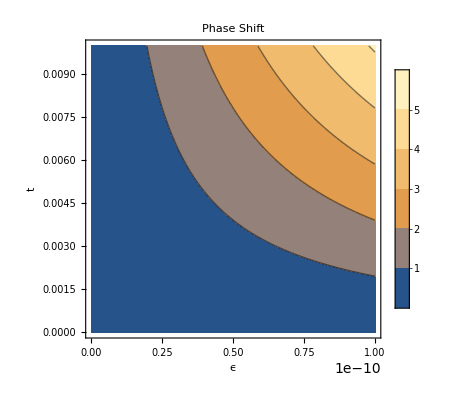

```mathematica
g=ContourPlot[f[ϵ,t],{ϵ,0,10^-10},{t,0,0.01},PlotLabel->"Phase Shift",AxesLabel->{"ϵ","t"},PlotLegends->Automatic]
```

```mathematica
1/(3*√(2*Pi))*(a1^2-a0^2)*ele^2/(4*Pi*e0*ħ)*T*√((m*ω)/ħ)
```

1.09616×10^11

```mathematica
ele^2/(4*Pi*e0*ħ)*(a0*a1*√((m*ω)/ħ))/(3*√(2*Pi))
```

7.30775×10^12

```mathematica
ele^2/(4*Pi*e0*ħ)*(5*a0*a1^2*√((m*ω)/ħ))/(672*√Pi)*T
```

2.06331×10^9

```mathematica
Clear[a0,a1,t]
```

```mathematica
((10 a0^2+a1^2) √((m ω)/ħ))/(30 √(2 π))*ele^2/(4*Pi*e0*ħ)*t*ϵ
```

5.11542×10^12 t ϵ

```mathematica
1.8269364951206487*^12 (1+9 p0) t ϵ
```

1.82694×10^12 (1+9 p0) t ϵ

```mathematica
Grad[1.8269364951206487*^12 (1+9 p0) t ϵ,{p0}]
```

{1.64424×10^13 t ϵ}

```mathematica
1.6442428456085838*^13 t ϵ*(dp0)
```

1.64424×10^13 dp0 t ϵ

```mathematica
((11 a0 a1^2 ele T √(m ω) ϵ̃)/(60 √π))/((ele T √(m ω) ϵ̃ (10 *a0^2+a1^2))/(30 √(2 π)))
```

```mathematica
(11 a0 a1^2)/(√2 (10 a0^2+a1^2))
```

(11 √(2/5))/7

```mathematica
N[(11 √(2/5))/7]
```

0.993859

```mathematica
N[(11 √(2/5))/7]
```

0.993859

```mathematica
((5 a0a1^2 ele^2 T √((m ω)/ħ) ϵ̃)/(2688 ħ π^(3/2)))/(((10 a0^2+a1^2) √((m ω)/ħ))/(30 √(2 π))*ele^2/(4*Pi*e0*ħ)*T*ϵ̃)
```

(2.79503×10^-12 a0a1^2)/(10 a0^2+a1^2)

```mathematica
ϵ̃ ele^2/(4π Subscript[ε, 0] ħ)(5 a0a1^2 √(mω/ħ))/(672 √π)T
```

(5 a0a1^2 ele^2 T √((m ω)/ħ) ϵ̃)/(2688 ħ π^(3/2))

```mathematica
(10 a0^2+a1^2)/(30 √(2π))ϵ̃ ele^2/(4π Subscript[ε, 0] ħ)√(mω/ħ)T
```

((10 a0^2+a1^2) ele^2 T √((m ω)/ħ) ϵ̃)/(120 √2 ħ π^(3/2))

```mathematica
((5 a0a1^2 ele^2 T √((m ω)/ħ) ϵ̃)/(2688 ħ π^(3/2)))/(((10 a0^2+a1^2) ele^2 T √((m ω)/ħ) ϵ̃)/(120 √2 ħ π^(3/2)))
```

(25 a0a1^2)/(56 √2 (10 a0^2+a1^2))

```mathematica
(25 a0*a1^2)/(56 √2 (10 a0^2+a1^2))
```

(5 √(5/2))/196

```mathematica
N[(5 √(5/2))/196]
```

0.0403352